```mathematica
u090494e　荒井直幸　2015年1月6日
```

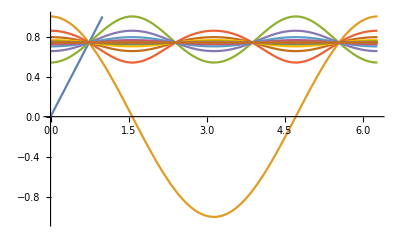

```mathematica
Plot[Evaluate[NestList[Cos,x,50]],{x,0,2 Pi},PlotRange->{-1.05,1}]
```

```mathematica
課題１
```

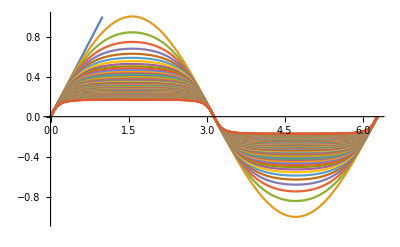

```mathematica
Plot[Evaluate[NestList[Sin,x,100]],{x,0,2 Pi},PlotRange->{-1.05,1}]
```

```mathematica
課題２
```

```mathematica
1)
```

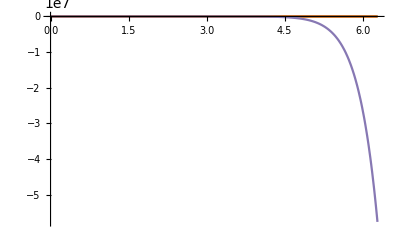

```mathematica
f1[x_]:=0.5 x (1-x);
Plot[Evaluate[NestList[f1,x,20]],{x,0,2 Pi},PlotRange->All]
```

```mathematica
2)
```

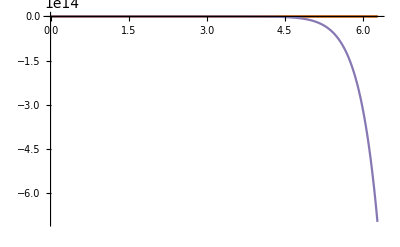

```mathematica
f2[x_]:=1.5 x (1-x);
Plot[Evaluate[NestList[f2,x,20]],{x,0,2 Pi},PlotRange->All]
```

```mathematica
3)
```

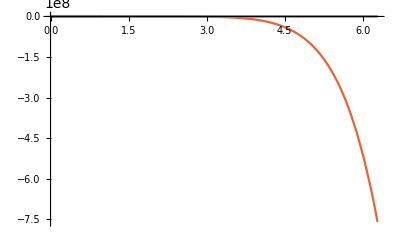

```mathematica
f3[x_]:=2.5 x (1-x);
Plot[Evaluate[NestList[f3,x,20]],{x,0,2 Pi},PlotRange->All]
```

```mathematica
4)
```

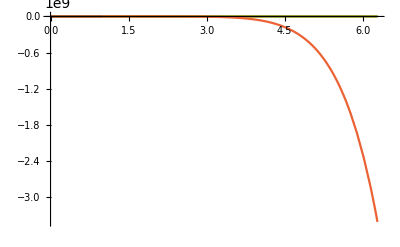

```mathematica
f4[x_]:=3.1 x (1-x);
Plot[Evaluate[NestList[f4,x,20]],{x,0,2 Pi},PlotRange->All]
```

```mathematica
5)
```

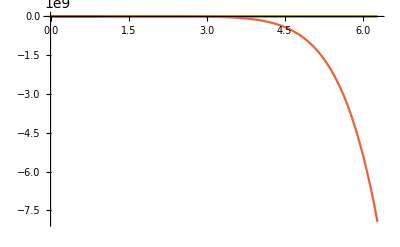

```mathematica
f5[x_]:=3.5 x (1-x);
Plot[Evaluate[NestList[f5,x,20]],{x,0,2 Pi},PlotRange->All]
```

```mathematica
6)
```

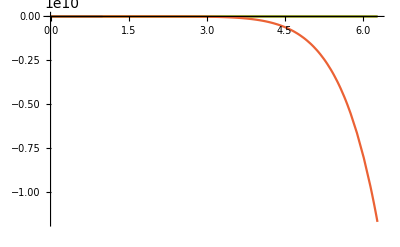

```mathematica
f6[x_]:=3.7 x (1-x);
Plot[Evaluate[NestList[f6,x,20]],{x,0,2 Pi},PlotRange->All]
```

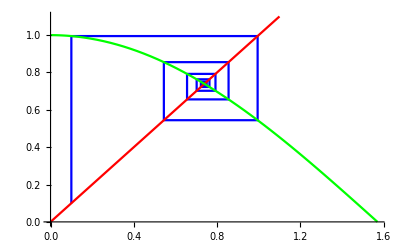

```mathematica
kazu={};
i=0;
shoki=0.1;
AppendTo[kazu,{shoki,shoki}];
While[i<100,
x1=Cos[shoki];
AppendTo[kazu,{shoki,x1}];
shoki=x1;
AppendTo[kazu,{shoki,x1}];
i++]
graph1=ListPlot[kazu,Joined->True,PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,0,1]];
graph2=Plot[x,{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[1,0,0]];
graph3=Plot[Cos[x],{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,1,0]];
Show[graph1,graph2,graph3]
```

```mathematica
課題３
```

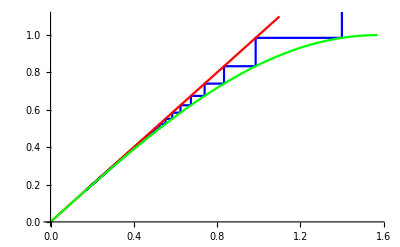

```mathematica
kazu1={};
i=0;
shoki1=1.4;
AppendTo[kazu1,{shoki1,shoki1}];
While[i<100,
x1=Sin[shoki1];
AppendTo[kazu1,{shoki1,x1}];
shoki1=x1;
AppendTo[kazu1,{shoki1,x1}];
i++]
graph4=ListPlot[kazu1,Joined->True,PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,0,1]];
graph5=Plot[x,{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[1,0,0]];
graph6=Plot[Sin[x],{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,1,0]];
Show[graph4,graph5,graph6]
```

```mathematica
課題４
```

```mathematica
a)
```

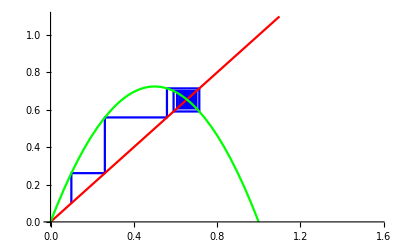

```mathematica
f7[x_]:=2.9 x (1-x);
kazu2={};
i=0;
shoki2=0.1;
AppendTo[kazu2,{shoki2,shoki2}];
While[i<100,
x1=f7[shoki2];
AppendTo[kazu2,{shoki2,x1}];
shoki2=x1;
AppendTo[kazu2,{shoki2,x1}];
i++]
graph7=ListPlot[kazu2,Joined->True,PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,0,1]];
graph8=Plot[x,{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[1,0,0]];
graph9=Plot[f7[x],{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,1,0]];
Show[graph7,graph8,graph9]
```

```mathematica
b)
```

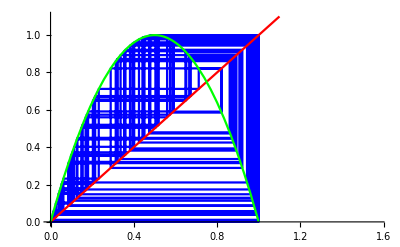

```mathematica
f8[x_]:=4 x (1-x);
kazu3={};
i=0;
shoki3=0.1;
AppendTo[kazu3,{shoki3,shoki3}];
While[i<100,
x1=f8[shoki3];
AppendTo[kazu3,{shoki3,x1}];
shoki3=x1;
AppendTo[kazu3,{shoki3,x1}];
i++]
graph10=ListPlot[kazu3,Joined->True,PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,0,1]];
graph11=Plot[x,{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[1,0,0]];
graph12=Plot[f8[x],{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,1,0]];
Show[graph10,graph11,graph12]
```

```mathematica
c)
```

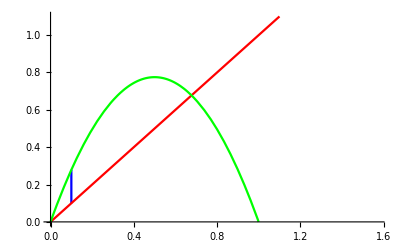

```mathematica
f9[x_]:=3.1 x (1-x);
kazu4={};
i=400;
shoki4=0.1;
AppendTo[kazu4,{shoki4,shoki4}];
While[i<500,
x1=f9[shoki4];
AppendTo[kazu4,{shoki4,x1}];
shoki3=x1;
AppendTo[kazu4,{shoki4,x1}];
i++]
graph13=ListPlot[kazu4,Joined->True,PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,0,1]];
graph14=Plot[x,{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[1,0,0]];
graph15=Plot[f9[x],{x,0,Pi/2},PlotRange->{{0,Pi/2},{0,1.1}},PlotStyle->RGBColor[0,1,0]];
Show[graph13,graph14,graph15]
```